LegendPosition::shdw: Symbol "LegendPosition" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

LegendSize::shdw: Symbol "LegendSize" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

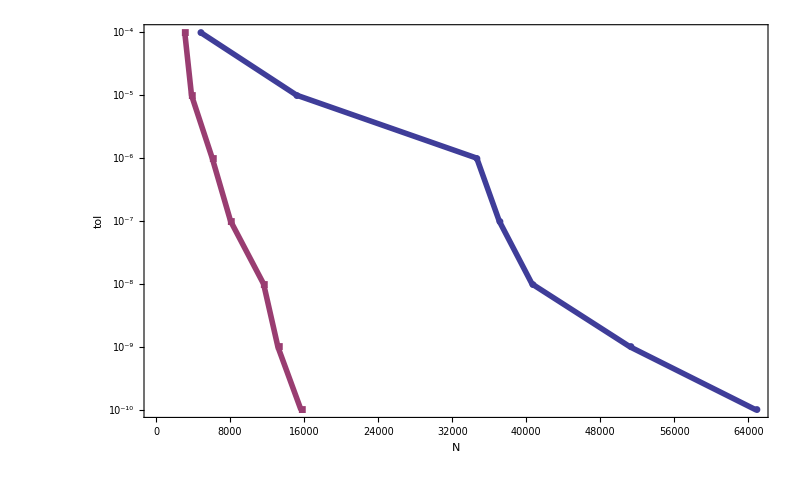

```mathematica
(*1_1*)
NN={4,5,6,7,8,9,10};
NN=10.^-#&/@NN;

simple={4782,15193,34652,37083,40628,51231,64823};
opress5={3104,3835,6074,8056,11627,13173,15666};
opress7={2788,3564,5978,6928,11008,13111,13852};
opress10={2895,3797,6076,6545,10436,12072,14811};
opress15={2947,3882,5773,7062,9712,12355,15790};
opress30={2789,4452,7189,6978,9694,13875,18785};

Needs["PlotLegends`"]
gp[NN_,arr_]:=Partition[Riffle[NN,arr],2];
(*gp[opress7,NN], gp[opress10,NN], gp[opress15,NN], gp[opress30,NN]*)
(* Style["OPR7",20,Bold], Style["OPR15",20,Bold], Style["OPR30",20,Bold]*)
g1=ListLogPlot[{gp[simple,NN],gp[opress5,NN]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["SP",20,Bold],Style["OPR5",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","tol"},LegendSize->0.5,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800, PlotRange->All]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_1.pdf",g1];
```

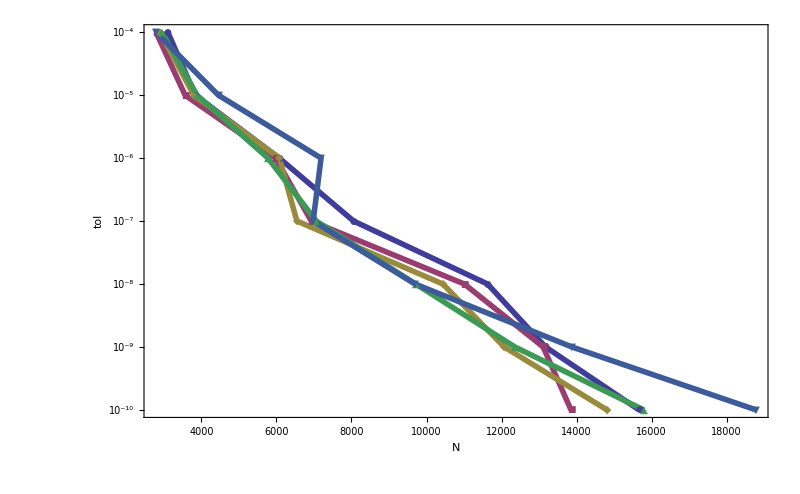

```mathematica
g2=ListLogPlot[{gp[opress5,NN], gp[opress7,NN], gp[opress10,NN], gp[opress15,NN], gp[opress30,NN]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["OPR5",20,Bold], Style["OPR7",20,Bold], Style["OPR10",20,Bold], Style["OPR15",20,Bold], Style["OPR30",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","tol"},LegendSize->0.7,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800, PlotRange->All]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_2.pdf",g2];
```

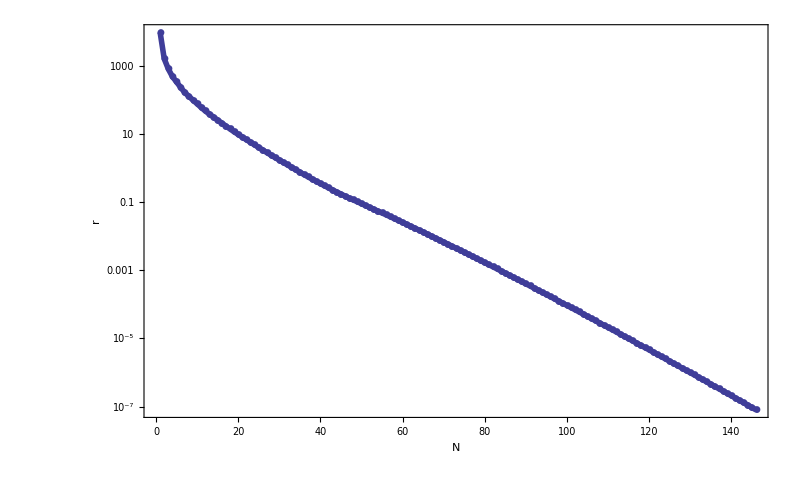

```mathematica
NN = Range[1, 146];
simple ={9744.050000000,1629.777100902,814.469003266,484.678050556,339.032366565,234.170243251,165.056630908,128.069573086,99.340479912,77.281403781,60.441016216,47.554367572,38.507430758,31.440047526,25.691000870,21.024600706,17.237625906,14.161359812,11.658371625,9.733637340,8.153024377,6.831828332,5.727899308,4.805405940,4.034194775,3.389055866,2.848997074,2.398095417,2.034449630,1.726004972,1.464586897,1.243169078,1.055727536,0.897108269,0.762909639,0.649379046,0.553322721,0.475254271,0.408953278,0.352323776,0.303916334,0.262495594,0.227243388,0.198341263,0.173242139,0.151420935,0.132428092,0.116552834,0.102671604,0.090420001,0.079606719,0.070231687,0.062052468,0.054774938,0.048307600,0.042567006,0.037477247,0.032969440,0.028981220,0.025490085,0.022400313,0.019666899,0.017251967,0.015121070,0.013242995,0.011589555,0.010135379,0.008857689,0.007736091,0.006752363,0.005890261,0.005135331,0.004474736,0.003897090,0.003392314,0.002951494,0.002566762,0.002231175,0.001938619,0.001683713,0.001461725,0.001268500,0.001100391,0.000954202,0.000827131,0.000716725,0.000620839,0.000537598,0.000465362,0.000402700,0.000348364,0.000301265,0.000260453,0.000225102,0.000194491,0.000167993,0.000145064,0.000125229,0.000108075,0.000093246,0.000080429,0.000069355,0.000059790,0.000051531,0.000044401,0.000038247,0.000032939,0.000028359,0.000024411,0.000021006,0.000018073,0.000015545,0.000013368,0.000011492,0.000009878,0.000008488,0.000007292,0.000006263,0.000005378,0.000004617,0.000003963,0.000003400,0.000002917,0.000002502,0.000002145,0.000001839,0.000001576,0.000001351,0.000001157,0.000000991,0.000000849,0.000000727,0.000000622,0.000000532,0.000000455,0.000000389,0.000000333,0.000000285,0.000000243,0.000000208,0.000000178,0.000000152,0.000000129,0.000000111,0.000000094,0.000000080};
g3=ListLogPlot[{simple},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.01]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["SP",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","r"},LegendSize->0.7,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800 , PlotRange->All]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_3.pdf",g3];
(*N=20, 146 iter*)
```

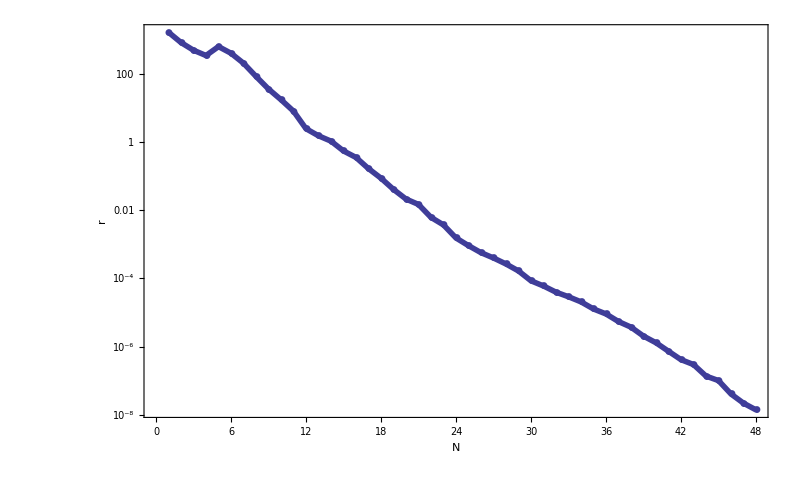

```mathematica
NN=Range[1, 48];(*48/44*)
oprR1={1629.777100902,814.469003266,484.678050556,339.032366565,619.063917224,395.381378049,201.776196208,82.922412087,35.383387483,17.212988464,7.939358267,2.428661583,1.506842921,1.050253058,0.542078815,0.349635540,0.164426297,0.086160065,0.040431353,0.021108896,0.014649993,0.006127236,0.003681971,0.001526674,0.000910296,0.000566731,0.000395917,0.000263938,0.000164951,0.000084868,0.000059867,0.000039364,0.000028916,0.000020507,0.000012682,0.000009063,0.000005425,0.000003718,0.000002033,0.000001296,0.000000731,0.000000415,0.000000298,0.000000137,0.000000101,0.000000041,0.000000022,0.000000014};
g4=ListLogPlot[{oprR1},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.01]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["OPR1",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","r"},LegendSize->0.7,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800 , PlotRange->All]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_4.pdf",g4];
```

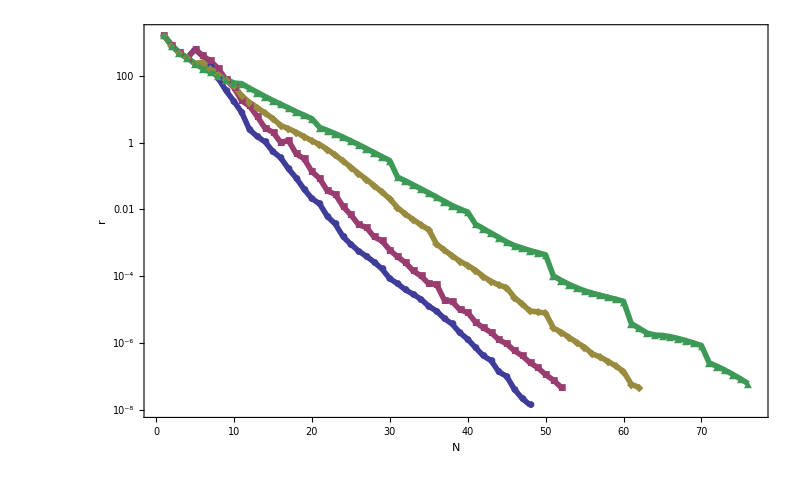

```mathematica
NN=Range[1, 52];(*52/24*)
oprR2={1629.777100902,814.469003266,484.678050556,339.032366565,619.063917224,392.560322330,276.595999441,163.481920968,76.145629539,44.121060302,17.834261633,12.445097023,5.971393415,2.690918374,2.046917893,1.012401045,1.149764446,0.454952813,0.329134924,0.135729151,0.084016483,0.035540502,0.028414233,0.012193662,0.006912200,0.003483538,0.002866150,0.001493963,0.001133965,0.000607226,0.000380330,0.000257699,0.000144545,0.000102281,0.000059806,0.000057581,0.000019414,0.000017490,0.000009886,0.000008239,0.000004205,0.000002862,0.000002079,0.000001250,0.000000949,0.000000591,0.000000416,0.000000257,0.000000183,0.000000113,0.000000078,0.000000047};
g5=ListLogPlot[{gp[Range[1, 48],oprR1],gp[Range[1, 52],oprR2], gp[Range[1, 62],oprR5], gp[Range[1, 76],oprR10]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.01]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["OPR1",20,Bold], Style["OPR2",20,Bold], Style["OPR5",20,Bold], Style["OPR10",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","r"},LegendSize->0.7,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800 , PlotRange->{{0.0,77},{0.00000001,2000}}]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_1_2.pdf",g5];
```

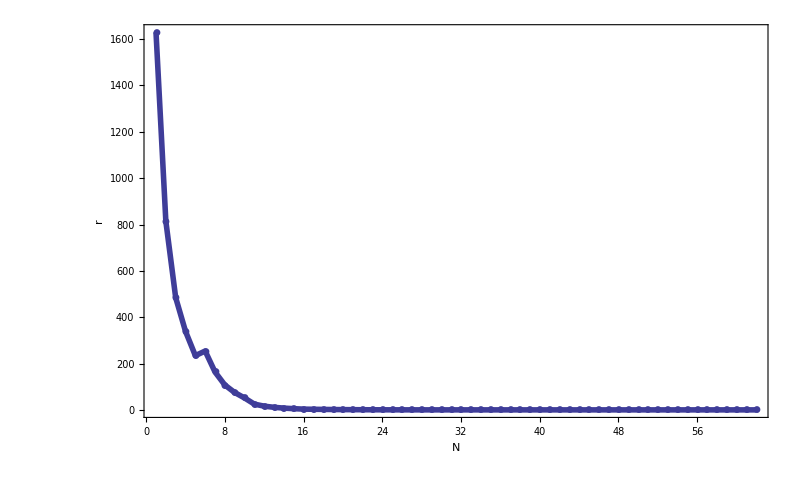

```mathematica
NN=Range[1, 52];(*62/12*)
oprR5={1629.777100902,814.469003266,484.678050556,339.032366565,234.170243251,253.972616549,163.584390564,107.265975894,74.894215440,51.452127194,24.846542111,16.013559778,11.088164140,7.626799321,5.219234433,3.239457750,2.602619270,2.020465664,1.516671445,1.127185664,0.875420359,0.618750434,0.422228150,0.280757277,0.183054089,0.118478249,0.078843185,0.051336459,0.032860784,0.020745773,0.011245586,0.007258013,0.004968073,0.003432180,0.002469332,0.000918911,0.000608234,0.000408577,0.000281688,0.000209158,0.000151022,0.000097425,0.000069918,0.000054603,0.000045634,0.000023079,0.000014704,0.000009073,0.000008540,0.000007890,0.000002830,0.000002105,0.000001488,0.000001041,0.000000748,0.000000477,0.000000380,0.000000285,0.000000205,0.000000142,0.000000058,0.000000047};
g7=ListPlot[{oprR5},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.01]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["OPR5",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","r"},LegendSize->0.7,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800 , PlotRange->All]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_7.pdf",g7];
```

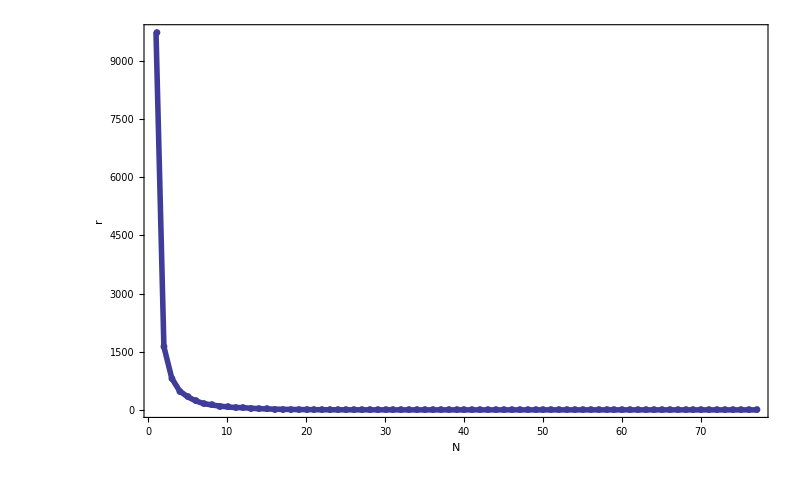

```mathematica
NN=Range[1, 77];(*77/7*)
oprR10={9744.050000000,1629.777100902,814.469003266,484.678050556,339.032366565,234.170243251,165.056630908,128.069573086,99.340479912,77.281403781,60.441016216,57.756873014,42.163298101,31.888559352,23.795765208,18.174787532,14.080494728,10.814387713,8.360791959,6.599753212,5.179680495,2.831305281,2.307609504,1.843791677,1.450391423,1.126805807,0.866655484,0.661139263,0.500999449,0.378334519,0.287615886,0.092716023,0.071327335,0.054405000,0.041224221,0.031080210,0.023345676,0.017490864,0.013083648,0.010275710,0.008294588,0.003610843,0.002665687,0.001962452,0.001442236,0.001059143,0.000827699,0.000695465,0.000586954,0.000507017,0.000433714,0.000102079,0.000075189,0.000057123,0.000045014,0.000036618,0.000030958,0.000026952,0.000023502,0.000020435,0.000017775,0.000003811,0.000002775,0.000002002,0.000001736,0.000001686,0.000001548,0.000001371,0.000001184,0.000001004,0.000000839,0.000000254,0.000000201,0.000000155,0.000000116,0.000000085,0.000000061};
g6=ListPlot[{oprR10},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.01]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["OPR10",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","r"},LegendSize->0.7,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800 , PlotRange->All]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_6.pdf",g6];
```

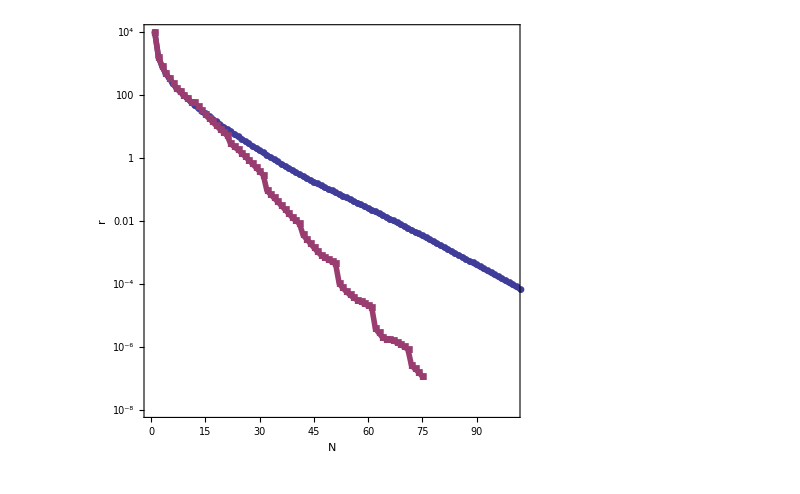

```mathematica
gSPWithOpr=ListLogPlot[{gp[Range[1, 147],simple], gp[Range[1, 76],oprR10]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.01]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["SP",20,Bold], Style["OPR5",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","r"},LegendSize->0.7,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800 , PlotRange->{{0.0,100},{0.00000001,10000}}]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_1_1.pdf",gSPWithOpr];
```